```mathematica
FilePath = NotebookDirectory[] <> "NROpsDD/";
Get[FilePath <> "TS.m"];
Get[FilePath <> "Y.m"];
```

LUX-Zeplin Test Statistic (TS)

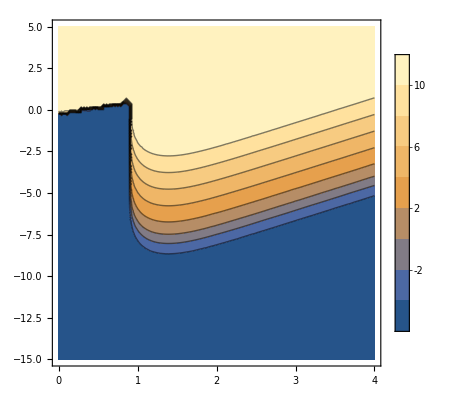

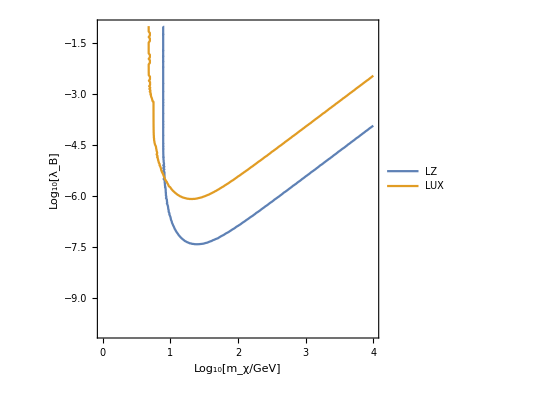

```mathematica
LZTS = Import[NotebookDirectory[] <> "LZ-TS.txt", "Table"];
xval = LZTS[[All,1]];
yval = LZTS[[All,2]];
zval = LZTS[[All, 3]];
nbins = 201;
data1 = Table[zval[[j + (i-1)*nbins]], {i, nbins}, {j,nbins}];
xval = xval[[1;;nbins^2;;nbins]];
yval = yval[[1;;nbins]];
myTS = ListInterpolation[data1, {xval, yval}, InterpolationOrder->{1,1}];

ContourPlot[Log10[myTS[10^mx,10^λ ]], {mx, 0, 4}, {λ, -15, 5}, PlotLegends->Automatic]
ContourPlot[{myTS[10^mx,10^λ ]==1.64, TS["LUX"][mx,λ]==1.64}, {mx, 0, 4}, {λ, -10, -1},PlotLegends->{"LZ", "LUX"}, FrameLabel->{"Log_10[m_χ/GeV]", "Log_10[λ_B]"}]
```

LUX-Zeplin Conversion Factors (Y)

InterpolatingFunction[{{1., 10000.}}, <>]

InterpolatingFunction[{{1., 10000.}}, <>]

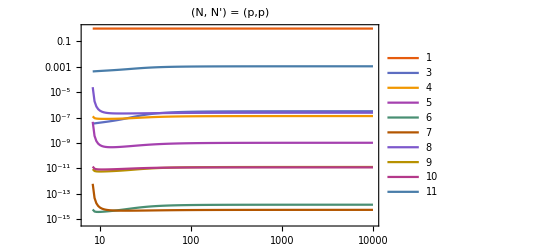

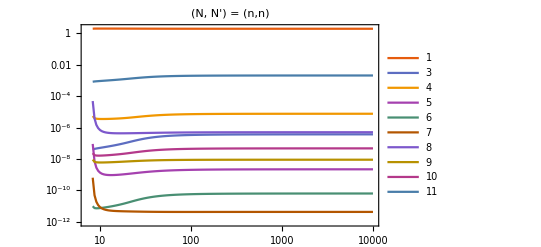

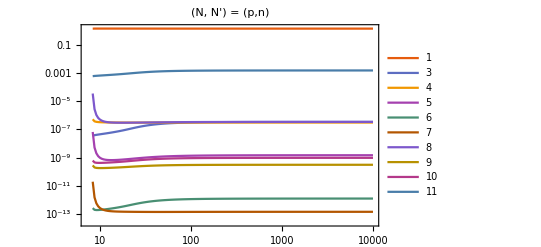

```mathematica
opvals = {1, 3, 4, 5, 6, 7, 8, 9, 10, 11};
LZYpp = Table[Import[NotebookDirectory[] <> "Y/Y_LZ_" <> ToString[i] <> ToString[i] <>"_pp.txt", "Table"], {i, opvals}];
LZYpn = Table[Import[NotebookDirectory[] <> "Y/Y_LZ_" <> ToString[i] <> ToString[i] <>"_pn.txt", "Table"], {i, opvals}];
LZYnn = Table[Import[NotebookDirectory[] <> "Y/Y_LZ_" <> ToString[i] <> ToString[i] <>"_nn.txt", "Table"], {i, opvals}];

LZYnnSD = Interpolation[LZYnn[[3]]]

LZYppSD = Interpolation[LZYpp[[3]]]

ListLogLogPlot[LZYpp, Joined-> True, PlotTheme->"Scientific", PlotLegends->opvals, PlotLabel->"(N, N') = (p,p)"]
ListLogLogPlot[LZYnn, Joined-> True, PlotTheme->"Scientific", PlotLegends->opvals, PlotLabel->"(N, N') = (n,n)"]
ListLogLogPlot[Abs[LZYpn], Joined-> True, PlotTheme->"Scientific", PlotLegends->opvals, PlotLabel->"(N, N') = (p,n)"]
```

Comparison with LUX conversion factors

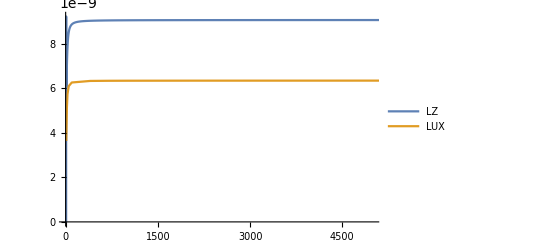

```mathematica
NRopsY = Table[{m, Y["Contact"]["LUX"][9,9]["n","n"][m]}, {m, {10,20,30,50,100,400,700,1000,2000,5000,10000}}];

ListPlot[{LZYnn[[8]], NRopsY},Joined->True, PlotLegends->{"LZ", "LUX"}]
```

Projected LZ limits on SD-neutron couplings

```mathematica
mN = 0.9315;
GeV2cm=1.97 10^-14;(* GeV to cm^-1 conversion factor *)
μ[mχ_,mN]:=mχ mN/(mχ+mN);
λSD[σSD_,mχ_]:=√(π σSD/(3 μ[mχ,mN]^2 GeV2cm^2))
```

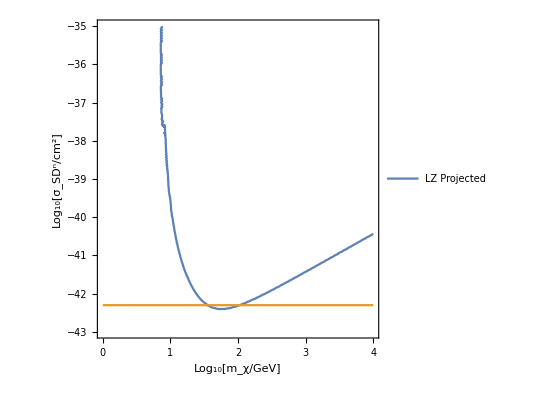

```mathematica
(*Be careful of SD limits - might need to add in correction for 2-body currents*)
ContourPlot[{myTS[10^lmx,16*(10^lmx)*mN*λSD[10^lσ, 10^lmx]*Sqrt[LZYnnSD[10^lmx]]]==2.71, lσ==Log10[5*^-43]}, {lmx, 0, 4}, {lσ, -43, -35},PlotLegends->{"LZ Projected"}, FrameLabel->{"Log_10[m_χ/GeV]", "Log_10[σ_SD^n/cm^2]"}]
```